#### Reading values from txt files

```mathematica
OldFile=Import["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/phi_ew_old.txt","Table"];
OldPosition=OldFile[[All,2]];
OldPhi=OldFile[[All,3]];
OldPhiError=OldFile[[All,4]];
OldSigma=OldFile[[All,5]];
OldSigmaError=OldFile[[All,6]];
NewFile=Import["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/phi_ew_corrected.txt","Table"];
NewPosition=NewFile[[All,2]];
NewPhi=NewFile[[All,3]]
NewPhiError=NewFile[[All,4]];
NewSigma=NewFile[[All,5]];
NewSigmaError=NewFile[[All,6]];
Radius=1;
Alpha={-45,135,-85,175,-135,-5,95,45};(*old values: {-57,123,-119,175,-147,0,66,33};*)

OldPhiList=Table[{OldPhi[[i]]*Pi/180,Radius},{i,Length[OldPhi]}] ;(*converting to radian and giving a fixed radius*)
NewPhiList=Table[{NewPhi[[i]]*Pi/180,Radius},{i,Length[NewPhi]}];
OldPosition=Thread[{OldPosition,Large}];
NewPosition=Thread[{NewPosition,Large}];
```

{-35.25,130.5,-71.25,156.8,-143.6,-2.782,105.8,51.94}

### Plotting of the polar plot

```mathematica
OldPhiPolarPlot=ListPolarPlot[List /@ OldPhiList, PlotMarkers->List/@OldPosition,PlotStyle->Large, PolarAxes->Automatic,PolarAxesOrigin->{0,Radius+0.2}, PolarTicks->{"Degrees",Automatic},TicksStyle->Medium,PlotRange->1.5,PolarGridLines->Automatic,PlotLabel->Style[TraditionalForm[HoldForm["Uncorrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large]
NewPhiPolarPlot=ListPolarPlot[List /@ NewPhiList, PlotMarkers->List/@NewPosition,PolarAxes->Automatic,PolarAxesOrigin->{0,Radius+0.2}, PolarTicks->{"Degrees",Automatic},TicksStyle->Medium,PlotRange->1.5,PolarGridLines->Automatic,PlotLabel->Style[TraditionalForm[HoldForm["Corrected " OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large]
```

-Graphics-

-Graphics-

### Plotting of the α-ϕ-Plot

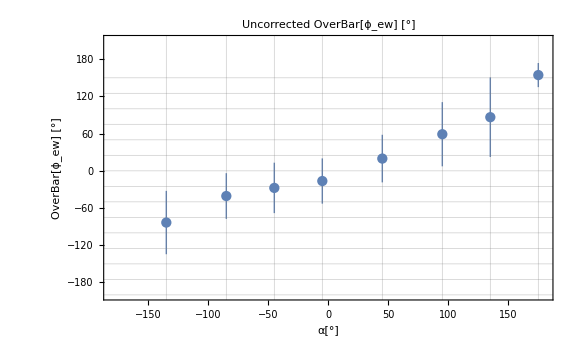

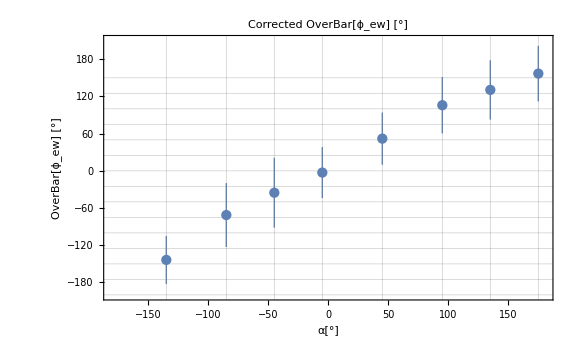

```mathematica
GridList=Table[i*25,{i,-200/25,150/25}];(*only for the graphic*)
OldAlphaPhiList=Table[{Alpha[[i]],Around[OldPhi[[i]],OldSigma[[i]]]},{i,Length[OldPhi]}];
OldAlphaPhiPlot=ListPlot[OldAlphaPhiList,PlotRange->{{-180,180},{-200,210}},GridLines->{Alpha,GridList}, Axes->False,Frame->True, FrameTicksStyle->Medium, FrameLabel->{Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Uncorrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large], ImageSize->Large]
NewAlphaPhiList=Table[{Alpha[[i]],Around[NewPhi[[i]],NewSigma[[i]]]},{i,Length[NewPhi]}];
NewAlphaPhiPlot=ListPlot[NewAlphaPhiList,PlotRange->{{-180,180},{-200,210}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameTicksStyle->Medium,FrameLabel->{Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large]
```

### Plotting the α-σ-Plot

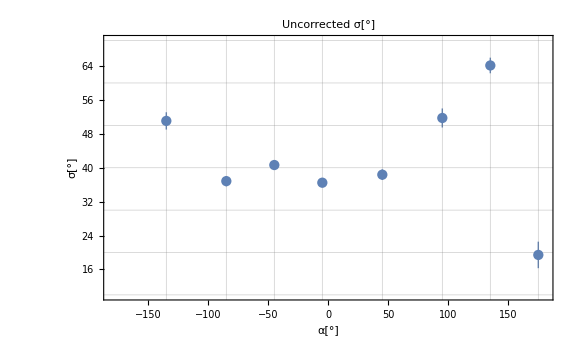

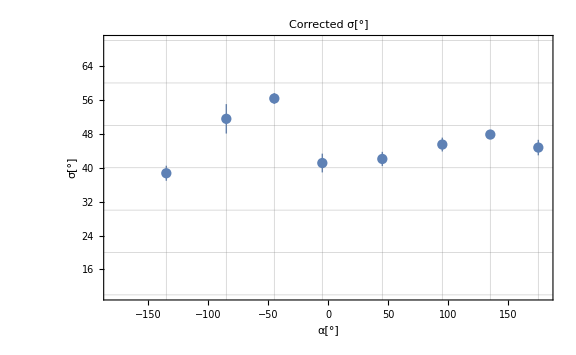

```mathematica
GridList=Table[i*10,{i,-200/25,150/10}];(*only for the graphic*)
OldAlphaSigmaList=Table[{Alpha[[i]],Around[OldSigma[[i]],OldSigmaError[[i]]]},{i,Length[OldSigma]}];
OldAlphaSigmaPlot=ListPlot[OldAlphaSigmaList,PlotRange->{{-180,180},{10,70}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameLabel->{"α[°]","σ[°]"},PlotLabel->Style["Uncorrected σ[°]",Large], ImageSize->Large]
NewAlphaSigmaList=Table[{Alpha[[i]],Around[NewSigma[[i]],NewSigmaError[[i]]]},{i,Length[OldSigma]}];
NewAlphaSigmaPlot=ListPlot[NewAlphaSigmaList,PlotRange->{{-180,180},{10,70}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameLabel->{"α[°]","σ[°]"},PlotLabel->Style["Corrected σ[°]",Large],ImageSize->Large]
```

### Saving graphics to file

```mathematica
column1=GraphicsColumn[{OldPhiPolarPlot ,NewPhiPolarPlot, OldAlphaPhiPlot ,OldAlphaSigmaPlot, NewAlphaPhiPlot ,NewAlphaSigmaPlot},ImageSize->Full];
Export["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/Results.pdf",column1,"PDF"]
Export["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/NewPhiPolarPlot.pdf",NewPhiPolarPlot,"PDF"]
Export["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/NewAlphaPhiPlot.pdf",NewAlphaPhiPlot,"PDF"]
Export["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/OldPhiPolarPlot.pdf",OldPhiPolarPlot,"PDF"]
Export["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/OldAlphaPhiPlot.pdf",OldAlphaPhiPlot,"PDF"]
```

/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/Results.pdf

/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/NewPhiPolarPlot.pdf

/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/NewAlphaPhiPlot.pdf

/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/OldPhiPolarPlot.pdf

/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/OldAlphaPhiPlot.pdf

## Klarifizierung des Konfidenzintervalls

FittedModel[2.37962+0.961784 α]

2.37962+0.961784 α-2.44691 √(139.327-0.0665046 α+0.00147788 α^2)

2.37962+0.961784 α+2.44691 √(139.327-0.0665046 α+0.00147788 α^2)

-32.9101

27.4793

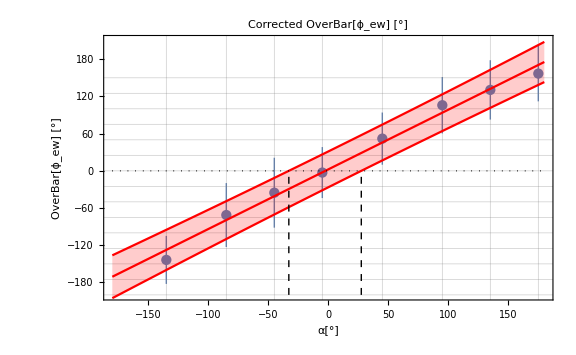

/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/ConfidencePlot.pdf

```mathematica
GridList=Table[i*25,{i,-200/25,150/25}];(*only for the graphic*)NewAlphaPhiPlot=ListPlot[NewAlphaPhiList,PlotRange->{{-180,180},{-200,210}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameLabel->{"α[°]",TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large];
NewAlphaPhiFitList=Table[{Alpha[[i]],NewPhi[[i]]},{i,Length[NewPhi]}];
fit=LinearModelFit[NewAlphaPhiFitList,α,α]
LowerPredictionBand=fit["SinglePredictionBands"][[1]]
UpperPredictionBand=fit["SinglePredictionBands"][[2]]

AssumedPhi=0;
MinimumAlpha=Solve[UpperPredictionBand==AssumedPhi,α][[1,1,2]]
MaximumAlpha=Solve[LowerPredictionBand==AssumedPhi,α][[1,1,2]]

ErrorGraphic=Show[NewAlphaPhiPlot,
Plot[{fit["BestFit"],fit["SinglePredictionBands"]},{α,-180,180},PlotStyle->Red,Filling->{2->{1},3->{1}}],
Graphics[{Dashed,Line[{{MinimumAlpha,-200},{MinimumAlpha,AssumedPhi}}]}],
Graphics[{Dashed,Line[{{MaximumAlpha,-200},{MaximumAlpha,AssumedPhi}}]}],
Graphics[{Dotted,Line[{{-180,0},{180,0}}]}]]
(*Export["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/ConfidencePlot.pdf",ErrorGraphic,"PDF"]*)
```

## Klarifizierung des Konfidenzintervalls 2

FittedModel[2.37962+0.961784 α]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.37962 | 4.01819 | 0.592212 | 0.57533
α | 0.961784 | 0.0384432 | 25.0183 | 2.68461×10^-7

45.9775

5.79923

-41.8408+0.961784 α

46.6+0.961784 α

-48.4517

43.5033

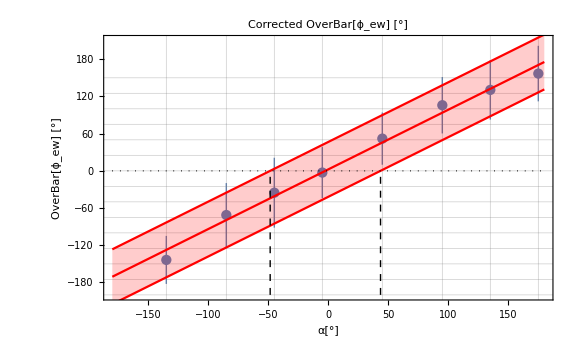

/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/ConfidencePlot.pdf

```mathematica
NewAlphaPhiPlot=ListPlot[NewAlphaPhiList,PlotRange->{{-180,180},{-200,210}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameTicksStyle->Medium,FrameLabel-> {Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large];
NewAlphaPhiFitList=Table[{Alpha[[i]],NewPhi[[i]]},{i,Length[NewPhi]}];
fit=LinearModelFit[NewAlphaPhiFitList,α,α]
fit["ParameterTable"]
MeanSigma=Mean[NewSigma]
StandardDeviation[NewSigma]
LowerPredictionBand=fit["BestFit"];
UpperPredictionBand=fit["BestFit"];
LowerPredictionBand=LowerPredictionBand-fit["BestFitParameters"][[2]]*MeanSigma
UpperPredictionBand=UpperPredictionBand+fit["BestFitParameters"][[2]]*MeanSigma

AssumedPhi=0;
MinimumAlpha=Solve[UpperPredictionBand==AssumedPhi,α][[1,1,2]]
MaximumAlpha=Solve[LowerPredictionBand==AssumedPhi,α][[1,1,2]]

ErrorGraphic=Show[ListPlot[NewAlphaPhiList,PlotRange->{{-180,180},{-200,210}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameTicksStyle->Medium,FrameLabel-> {Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large],
Plot[{fit["BestFit"],LowerPredictionBand,UpperPredictionBand},{α,-180,180},PlotStyle->Red,Filling->{2->{1},3->{1}}],
Graphics[{Dashed,Line[{{MinimumAlpha,-200},{MinimumAlpha,AssumedPhi}}]}],
Graphics[{Dashed,Line[{{MaximumAlpha,-200},{MaximumAlpha,AssumedPhi}}]}],
Graphics[{Dotted,Line[{{-180,0},{180,0}}]}],
PlotLabels->"Expressions"]
Export["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/ConfidencePlot.pdf",ErrorGraphic,"PDF"]
```